# Night 5 Part 2

### Defining Variables

```mathematica
Clear[f, density, xmin1, xmax1, ymin1, ymax1]
f = 2*((x/2)^2);
density =300;
ballastmass = 5000;
xmin1 = -2;
xmax1 = 2;
ymin1 = 0;
ymax1 = 2;
zmin1 = 0;
zmax1 =10;
xballast = 0;
yballast = 0;
```

### 3D Plot of Boat

```mathematica
RegionPlot3D[zmin1≤z≤zmax1&&f≤y≤ymax1&&xmin1≤x≤xmax1, {x, xmin1, xmax1},{y, ymin1, ymax1},{z, zmin1, zmax1}, PlotPoints->100,  Axes->True, AxesLabel->{x, y, z}]
```

-Graphics3D-

### Defining Boat region

```mathematica
boat = ImplicitRegion[f<y<ymax1&&xmin1<x<xmax1&&ymin1<y<ymax1, {x,y}]
```

ImplicitRegion[x^2/2<y<2&&-2<x<2&&0<y<2,{x,y}]

### Defining water region

```mathematica
water = ImplicitRegion[ymin1<y<d&&xmin1<x<xmax1&&ymin1<y<ymax1, {x,y}]
```

ImplicitRegion[0<y<d&&-2<x<2&&0<y<2,{x,y}]

### Defining Submerged region of boat as intersection of boat and water

```mathematica
submerged = RegionIntersection[boat, water]
```

ImplicitRegion[-2<x<2&&0<y<2&&0<y<d&&x^2/2<y<2,{x,y}]

### Manipulate plot where you can adjust draft

```mathematica
Manipulate[RegionPlot[{water/.{d->dd}, boat, submerged/.{d->dd}}, AspectRatio->Automatic],{{dd, 1, "draft"}, 0, 2, Appearance->"Labeled"}]
```

RegionPlot::argr: RegionPlot called with 1 argument; 3 arguments are expected.

### Figuring out total mass of boat by integration and adding ballastmass

∈ sign is escape, e, l, escape

```mathematica
boatmass = 10*Integrate[density,{x, y}∈boat]
```

16000

```mathematica
totalmass = boatmass+ballastmass
```

21000

### Finding COMs

```mathematica
xcomboat = ( 1/boatmass)*10*Integrate[x*density,{x, y}∈boat]
```

0

Just boat

```mathematica
ycomboat = N[( 1/boatmass)*10*Integrate[y*density,{x, y}∈boat]]
```

1.2

COM of combined boat and ballast: 2 ways, second one takes into account ballast x or y coordinate

```mathematica
xcom = N[( 1/totalmass)*10*Integrate[x*density,{x, y}∈boat]]
xcom = 1/(total)*(xcomboat*boatmass+xballast*ballastmass)
```

0.

0

```mathematica
ycom = N[( 1/totalmass)*10*Integrate[y*density,{x, y}∈boat]]
ycom = 1/(totalmass)*(ycomboat*boatmass+yballast*ballastmass)
```

0.914286

0.914286

### Finding Buoyant force with d as a variable

```mathematica
displacement = 10*Integrate[1000,{x, y}∈submerged, Assumptions->{ymin1<d<ymax1}]
```

40000/3 √2 d^(3/2)

### Figuring out waterline based on displacement

```mathematica
waterline = NSolve[displacement == mass, d, Reals]
```

{{d→1.07443}}

### With flat waterline, there is only one answer that satisfies the condition

```mathematica
draft = N[d/.waterline[[1]]]
```

1.07443

### Finding Center of buoyancy

```mathematica
cob = 10*Integrate[1000*{x, y}, {x,y}∈submerged, Assumptions->{ymin1<d<ymax1}]/displacement
```

{0,(3 d)/5}

```mathematica
cob/.{d->draft}
```

{0,0.644656}

```mathematica
ycob = cob[[2]]
```

(3 d)/5

### Plotting boat with waterline

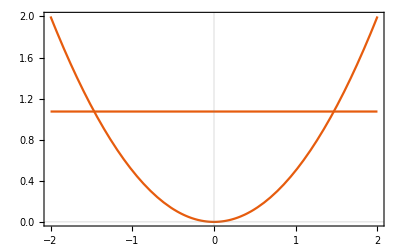

```mathematica
Show[Plot[f, {x,xmin1,xmax1},PlotRange->{{xmin1,xmax1},{ymin1,ymax1}}, PlotTheme->"Scientific"],Plot[draft, {x,xmin1,xmax1},PlotRange->{{xmin1,xmax1},{ymin1,ymax1}}, PlotTheme->"Scientific"] ]
```

```mathematica
10*(1/totalmass)Integrate[Integrate[1000*y, {y, 2*(x/2)^2,draft}],{x, -(2*draft)^(1/2), (2*draft)^(1/2)}]
```

0.644656